```mathematica
csvInput =Import["/Users/hans/Library/Developer/Xcode/DerivedData/SaturatorAU-amdvlwjrpoobljbrfarqbuoniwsc/Build/Products/Debug/arrayOut.csv"];
sound = ListPlay[#[[2]]&/@csvInput,SampleRate->48000,PlayRange->All];
Export["~/Desktop/test.wav",sound,SampleDepth->"Integer32"]
```

~/Desktop/test.wav

~/Desktop/test.wav

```mathematica
ListLinePlot[csvInput,PlotRange->All]
```

-Graphics-

## Short plot

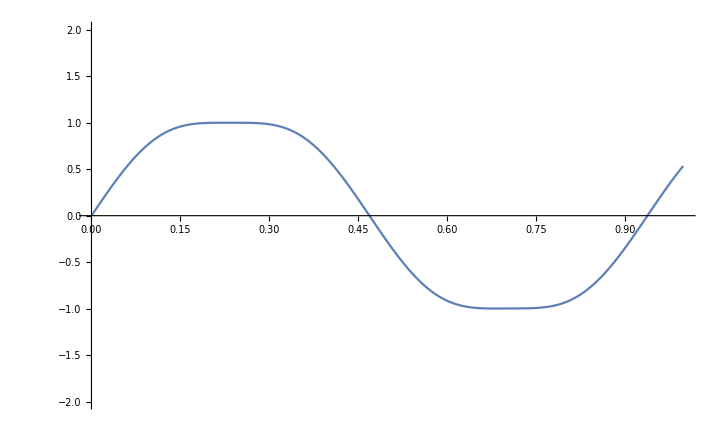

```mathematica
csvInput =Import["/Users/hans/Library/Developer/Xcode/DerivedData/SaturatorAU-amdvlwjrpoobljbrfarqbuoniwsc/Build/Products/Debug/arrayOut.csv"];
ListLinePlot[csvInput,PlotRange->2{-1,1}]
```